```mathematica
(*ρ[x1_,x2_]:=Sqrt[(x1^2 + x2^2) + γ^2*σ^4 /R^2- 2*γ*σ^2/R*(x1*Cos[ψ] + x2*Sin[ψ])]*)
ClearAll[γ ,R,σ,ψ ];
ρ[x1_,x2_]:=Sqrt[(x1-γ σ^2/R Cos[ψ] )^2 + (x2-γ σ^2/R Sin[ψ])^2 ]
```

### Nulcline plot for uniform density on the ring .

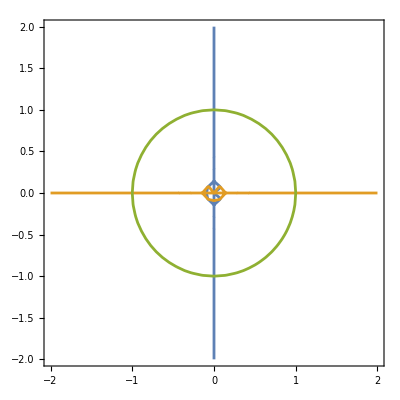

```mathematica
γ = 0;
R = 1;
σ = 0.705;
ψ =2 π/3;
ρ[x1_,x2_]:=Sqrt[(x1-γ σ^2/R Cos[ψ] )^2 + (x2-γ σ^2/R Sin[ψ])^2 ]
ContourPlot[{-x1 + R/ρ[x1,x2] BesselI[1,R/σ^2ρ[x1,x2]]/BesselI[0,R/σ^2ρ[x1,x2]](x1-γ σ^2/R Cos[ψ] )==0,
-x2 + R/ρ[x1,x2] BesselI[1,R/σ^2ρ[x1,x2]]/BesselI[0,R/σ^2ρ[x1,x2]](x2-γ σ^2/R Sin[ψ] )==0,x1^2+x2^2==1},
 {x1,-2.,2.},{x2,-2.,2.}]
```

### Nulcline plot for non uniform density on the ring.

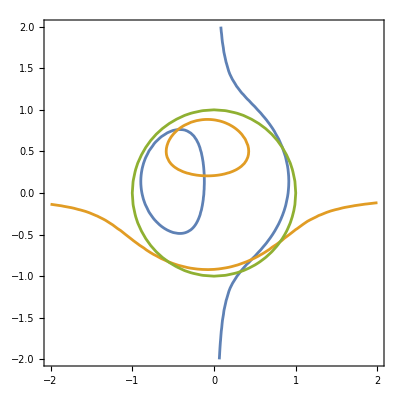

```mathematica
γ = 1;
R = 1;
σ = 0.4;
ψ =2 π/3;
ρ[x1_,x2_]:=Sqrt[(x1-γ σ^2/R Cos[ψ] )^2 + (x2-γ σ^2/R Sin[ψ])^2 ]
ContourPlot[{-x1 + R/ρ[x1,x2] BesselI[1,R/σ^2ρ[x1,x2]]/BesselI[0,R/σ^2ρ[x1,x2]](x1-γ σ^2/R Cos[ψ] )==0,
-x2 + R/ρ[x1,x2] BesselI[1,R/σ^2ρ[x1,x2]]/BesselI[0,R/σ^2ρ[x1,x2]](x2-γ σ^2/R Sin[ψ] )==0,x1^2+x2^2==1},
 {x1,-2.,2.},{x2,-2.,2.}]
```

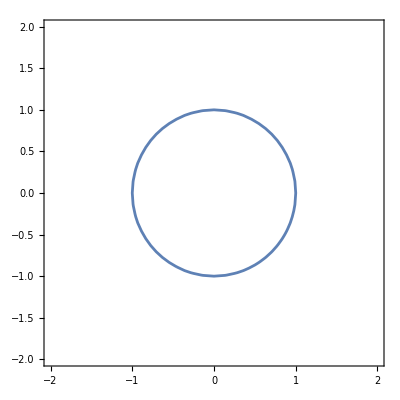
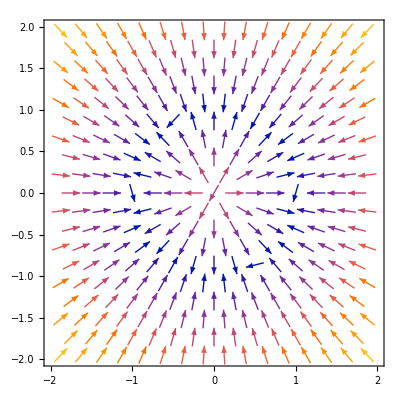

```mathematica
γ = 2;
R = 1;
σ = 0.01;
ψ =1 π/3;
ρ[x1_,x2_]:=Sqrt[(x1-γ σ^2/R Cos[ψ] )^2 + (x2-γ σ^2/R Sin[ψ])^2 ]
SP1 = ContourPlot[{x1^2+x2^2==R ^2},{x1,-2.,2.},{x2,-2.,2.}];
SP2 = VectorPlot[{-x1 + R/ρ[x1,x2] BesselI[1,R/σ^2ρ[x1,x2]]/BesselI[0,R/σ^2ρ[x1,x2]](x1-γ σ^2/R Cos[ψ] ),
-x2 + R/ρ[x1,x2] BesselI[1,R/σ^2ρ[x1,x2]]/BesselI[0,R/σ^2ρ[x1,x2]](x2-γ σ^2/R Sin[ψ] )},
 {x1,-2.,2.},{x2,-2.,2.}];
Overlay[{SP1,SP2}]
```

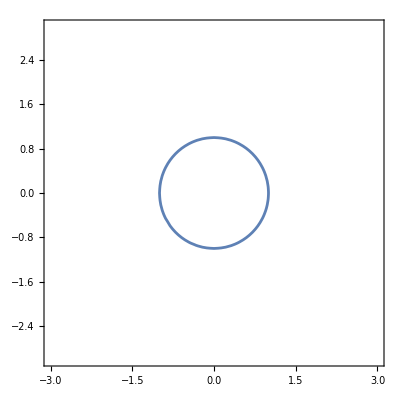

```mathematica
γ = 0;
R = 1;
σ = 0.0001;
ψ = π/4;
ρ[x1_,x2_]:=Sqrt[(x1-γ σ^2/R Cos[ψ] )^2 + (x2-γ σ^2/R Sin[ψ])^2 ]
ContourPlot[ρ[x1,x2] ==1,
 {x1,-3,3},{x2,-3,3}]
```

```mathematica
ContourPlot[x^2+y^2==1, {x,-2,2},{y,-2,2}]
```

-Graphics-

```mathematica
ContourPlot[x^2+y^2==1, {x,-2,2},{y,-2,2}]
```

```mathematica
Integrate[Exp[A Cos[θ]+B Sin[θ]+C],{θ,0,2π}]
```

ConditionalExpression[2 ⅇ^C π BesselI[0,√(A^2+B^2)], A∈ℝ&&B∈ℝ]

```mathematica
Integrate[Cos[θ]Exp[A Cos[θ]+B Sin[θ]+C],{θ,0,2π}]
Integrate[Sin[θ]Exp[A Cos[θ]+B Sin[θ]+C],{θ,0,2π}]
```

∫_0^(2 π) ⅇ^(C+A Cos[θ]+B Sin[θ]) Cos[θ]ⅆθ

$Aborted

```mathematica
Integrate[Exp[A Cos[θ]],{θ,0,2π}]
```

2 π BesselI[0,A]

```mathematica
Integrate[Sin[θ]Exp[A Cos[θ]],{θ,0,2π}]
```

0

```mathematica
Integrate[Cos[θ]Exp[A Cos[θ]],{θ,0,2π}]
```

2 π BesselI[1,A]

```mathematica
Integrate[Sin[2θ]Exp[A Cos[θ]],{θ,0,2π}]
```

0

```mathematica
Integrate[Cos[k θ]Exp[A Cos[θ]],{θ,0,2π}]
```

∫_0^(2 π) ⅇ^(A Cos[θ]) Cos[k θ]ⅆθ

```mathematica
D[BesselI[0,√(A^2+B^2)],A]
```

(A BesselI[1,√(A^2+B^2)])/(√(A^2+B^2))

```mathematica
FullSimplify[D[BesselI[0,√(A^2+B^2)],{A,2}]]
```

(2 A^2 BesselI[0,√(A^2+B^2)]+(-A^2+B^2) Hypergeometric0F1Regularized[2,1/4 (A^2+B^2)])/(2 (A^2+B^2))

```mathematica
Simplify[D[x1/√(x1^2+x2^2),x1]]
```

x2^2/((x1^2+x2^2)^(3/2))

```mathematica
Simplify[D[x2/√(x1^2+x2^2),x1]]
```

-(x1 x2)/((x1^2+x2^2)^(3/2))

```mathematica
Simplify[D[√(x1^2+x2^2),x1]]
```

x1/(√(x1^2+x2^2))

```mathematica
Simplify[D[BesselI[1,x1],x1]]
```

1/2 (BesselI[0,x1]+BesselI[2,x1])

```mathematica
Simplify[D[(x1 Cos[ψ]+x2 Sin[ψ])/√(x1^2+x2^2),x1]]
```

(x2 (x2 Cos[ψ]-x1 Sin[ψ]))/((x1^2+x2^2)^(3/2))

```mathematica
Simplify[D[(x1 Cos[ψ]+x2 Sin[ψ])/√(x1^2+x2^2),x2]]
```

(x1 (-x2 Cos[ψ]+x1 Sin[ψ]))/((x1^2+x2^2)^(3/2))

```mathematica
Simplify[D[(x1 Cos[ψ]+x2 Sin[ψ])/√(x1^2+x2^2)BesselI[1,R √(x1^2+x2^2)/σ^2],x1]]
```

1/(2 (x1^2+x2^2)^(3/2) σ^2)(2 x2 σ^2 BesselI[1,(R √(x1^2+x2^2))/σ^2] (x2 Cos[ψ]-x1 Sin[ψ])+R x1 √(x1^2+x2^2) BesselI[0,(R √(x1^2+x2^2))/σ^2] (x1 Cos[ψ]+x2 Sin[ψ])+R x1 √(x1^2+x2^2) BesselI[2,(R √(x1^2+x2^2))/σ^2] (x1 Cos[ψ]+x2 Sin[ψ]))

```mathematica
Simplify[D[(x1 Cos[ψ]+x2 Sin[ψ])/√(x1^2+x2^2)BesselI[1,R √(x1^2+x2^2)/σ^2],x2]]
```

1/(2 (x1^2+x2^2)^(3/2) σ^2)(2 x1 σ^2 BesselI[1,(R √(x1^2+x2^2))/σ^2] (-x2 Cos[ψ]+x1 Sin[ψ])+R x2 √(x1^2+x2^2) BesselI[0,(R √(x1^2+x2^2))/σ^2] (x1 Cos[ψ]+x2 Sin[ψ])+R x2 √(x1^2+x2^2) BesselI[2,(R √(x1^2+x2^2))/σ^2] (x1 Cos[ψ]+x2 Sin[ψ]))

```mathematica
D[Cos[θ-ψ],θ]
```

-Sin[θ-ψ]